```mathematica
pde=D[ψ[x,y], x,x]+D[ψ[x,y], y,y]-ⅇ^-x(x-2+y^3+6y)==0
```

-ⅇ^-x (-2+x+6 y+y^3)+ψ^(0,2)[x,y]+ψ^(2,0)[x,y]==0

```mathematica
DSolve[{
pde,
ψ[0,y]==y^3,
ψ[1,y]==(1+y^3)/ⅇ,
ψ[x,0]==x ⅇ^-x,
ψ[x,1]==ⅇ^-x(x+1)
},ψ[x,y],{x,y}]
```

DSolve[{-ⅇ^-x (-2+x+6 y+y^3)+ψ^(0,2)[x,y]+ψ^(2,0)[x,y]==0,ψ[0,y]==y^3,ψ[1,y]==(1+y^3)/ⅇ,ψ[x,0]==ⅇ^-x x,ψ[x,1]==ⅇ^-x (1+x)},ψ[x,y],{x,y}]

```mathematica
ψa[x_,y_]:=ⅇ^-x(x+y^3)
```

```mathematica
D[ψa[x,y], x]//FullSimplify
```

-ⅇ^-x (-1+x+y^3)

```mathematica
dψadx[x_,y_]:=-ⅇ^-x (-1+x+y^3)
```

```mathematica
D[ψa[x,y], y]//FullSimplify
```

3 ⅇ^-x y^2

```mathematica
dψady[x_,y_]:=3 ⅇ^-x y^2
```

```mathematica
D[ψa[x,y], x,x]//FullSimplify
```

ⅇ^-x (-2+x+y^3)

```mathematica
d2ψadx2[x_,y_]:=ⅇ^-x (-2+x+y^3)
```

```mathematica
D[ψa[x,y], x,y]//FullSimplify
```

-3 ⅇ^-x y^2

```mathematica
d2ψadxdy[x_,y_]:=-3 ⅇ^-x y^2
```

```mathematica
D[ψa[x,y], y,x]//FullSimplify
```

-3 ⅇ^-x y^2

```mathematica
d2ψadydx[x_,y_]:=-3 ⅇ^-x y^2
```

```mathematica
D[ψa[x,y], y,y]//FullSimplify
```

6 ⅇ^-x y

```mathematica
d2ψady2[x_,y_]:=6 ⅇ^-x y
```

```mathematica
Plot3D[ψa[x,y],{x,0,1},{y,0,1},
AxesLabel->{"x","y","ψ_a(x,y)"},PlotLabel->"Problem 5 analytical solution (compare to Lagaris (1998), Figure 8)"]
```

-Graphics3D-

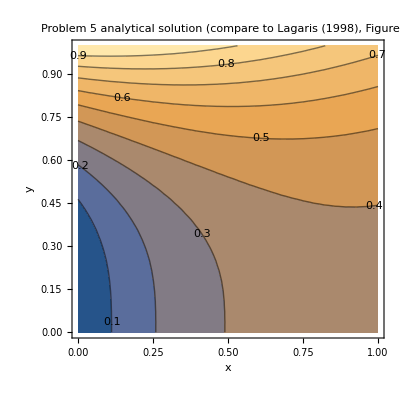

```mathematica
ContourPlot[ψa[x,y],{x,0,1},{y,0,1},
AxesLabel->{"x","y","ψ_a(x,y)"},PlotLabel->"Problem 5 analytical solution (compare to Lagaris (1998), Figure 8)",ContourLabels->True]
```

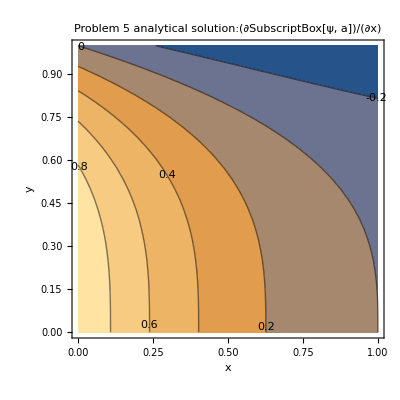

```mathematica
ContourPlot[dψadx[x,y],{x,0,1},{y,0,1},
AxesLabel->{"x","y","∂ψ_a/∂x"},PlotLabel->"Problem 5 analytical solution:(∂SubscriptBox[ψ, a])/(∂x)",ContourLabels->True]
```

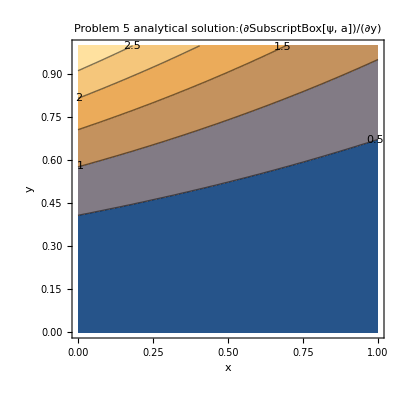

```mathematica
ContourPlot[dψady[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y","∂ψ_a/∂y"},PlotLabel->"Problem 5 analytical solution:(∂SubscriptBox[ψ, a])/(∂y)",ContourLabels->True]
```

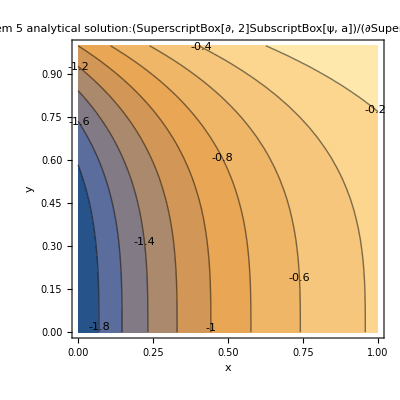

```mathematica
ContourPlot[d2ψadx2[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y","∂^2 ψ_a/∂x^2"},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]SubscriptBox[ψ, a])/(∂SuperscriptBox[x, 2])",ContourLabels->True]
```

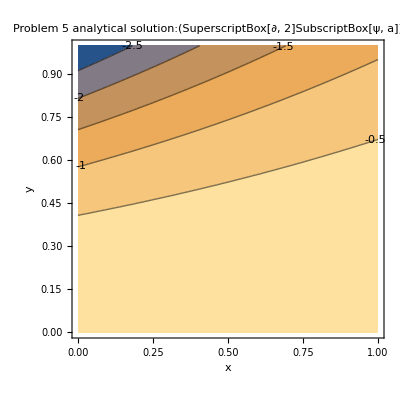

```mathematica
ContourPlot[d2ψadxdy[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y","∂^2 ψ_a/∂x∂y"},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]SubscriptBox[ψ, a])/(∂x ∂y)",ContourLabels->True]
```

```mathematica
ContourPlot[d2ψadydx[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y","∂^2 ψ_a/∂y∂x"},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]SubscriptBox[ψ, a])/(∂y ∂x)",ContourLabels->True]
```

-Graphics-

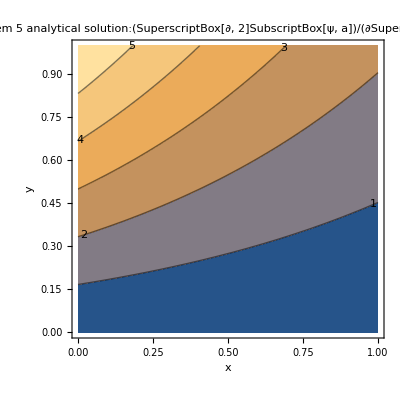

```mathematica
ContourPlot[d2ψady2[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y","∂^2 ψ_a/∂y^2"},AxesLabel->{"x","y","∂^2 ψ_a/∂x∂y"},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]SubscriptBox[ψ, a])/(∂SuperscriptBox[y, 2])",ContourLabels->True]
```